```mathematica
Manipulate[
Row[
{
Graphics[
{
EdgeForm[{Thick,Black}],LightBlue,Disk[{0,0},(b+a),{0,Pi}],
White,Disk[{-a,0}, b,{0,Pi}],Disk[{b,0}, a,{0,Pi}]
},
ImageSize->{250,250}
],
Graphics[
{
EdgeForm[{Thick,Black}],LightBlue,Disk[{b-a,Sqrt[a b]},Sqrt[a b]],
Opacity[0],
White,Disk[{0,0},(b+a),{0,Pi}],
White,Disk[{-a,0}, b,{0,Pi}],Disk[{b,0}, a,{0,Pi}]
},
ImageSize->{250,250}
]
}
],
{{a,8},1,10,1},
{{b,5},1,9,1}
]
```

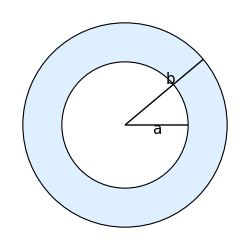
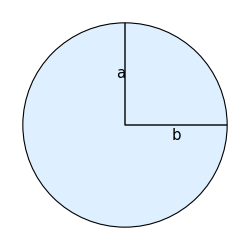

```mathematica
Row[
{
Graphics[
{
LightBlue,EdgeForm[{Thick,Black}],Disk[{0,0},1+Sqrt[5]],
White,Disk[{0,0},2],
Black,Thick,Line[{{0,0},{2,0}}],
Rotate[Line[{{0,0},{1+Sqrt[5],0}}],40 Degree,{0,0}],
Text[Style[a,15,Italic],{1,-.15}],
Text[Style[b,15,Italic],{1.45,1.45}]
},
ImageSize->{250,250}
],
Graphics[
{
LightBlue,EdgeForm[{Thick,Black}],Disk[{0,0},{1+Sqrt[5],2}],
Black,Thick,Line[{{0,2},{0,0},{1+Sqrt[5],0}}],
Text[Style[a,15,Italic],{-.15,1}],
Text[Style[b,15,Italic],{(1+Sqrt[5])/2,-.2}]
},
ImageSize->{250,250}
]
}
]
```

```mathematica
ellipses[a_,b_,number_]:=
Graphics[
Table[
Rotate[
{Hue[k/number],Thick,Circle[{0,0},{a,b}]},(*thing to rotate*)
k Pi/number,(*amount of rotation*)
{0,0}(*center of rotation*)
],
{k,0,number-1,1}
]
]
```

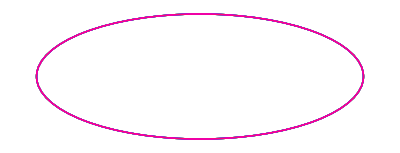

```mathematica
ellipses[13,5,12]
```

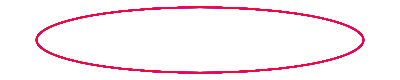

```mathematica
ellipses[21,3,40]
```

```mathematica
Manipulate[
Graphics[
Table[
Rotate[
{Hue[k/n],Thick,Circle[{0,0},{a,b}]},(*thing to rotate*)
k Pi/n,(*amount of rotation*)
{0,0}(*center of rotation*)
],
{k,0,n-1,1}
]
],
{{a,21},0,40,Appearance->"Labeled"},
{{b,13},0,20,Appearance->"Labeled"},
{{n,34},0,50,Appearance->"Labeled"}
]
```

Using the logic of ellipses[] instead of the function itself removes the extra step of having to run the ellipses function. This way when you reload Mathematica, you don’t have to re-run the ellipses function every time.